# Pango analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/pango-countries

```mathematica
dataset="pango-countries";
```

```mathematica
model="GARW";
```

```mathematica
imageSize=300;
```

```mathematica
gridCount=1;
```

## Setup

### Date ticks

```mathematica
dateTicks={"2021-10-01","2021-11-01","2021-12-01","2022-01-01","2022-02-01","2022-03-01","2022-04-01","2022-05-01","2022-06-01","2022-07-01","2022-08-01","2022-09-01","2022-10-01"};
```

### Countries

```mathematica
countriesToDrop={};
```

## Variants and colors

### Import

```mathematica
variantData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=variantData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
variantData=Drop[variantData,1];
```

```mathematica
variants=Union[variantData[[All,3]]]
```

{B.1.1.529,BA.2,BA.2.12,BA.2.12.1,BA.2.13,BA.2.13.1,BA.2.18,BA.2.3,BA.2.38,BA.2.56,BA.2.75,BA.2.75.1,BA.2.75.2,BA.2.75.5,BA.2.76,BA.2.9,BA.4,BA.4.1,BA.4.1.1,BA.4.1.6,BA.4.1.8,BA.4.2,BA.4.3,BA.4.4,BA.4.6,BA.5,BA.5.1,BA.5.10.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.19,BA.5.1.2,BA.5.1.21,BA.5.1.3,BA.5.1.5,BA.5.1.6,BA.5.1.7,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.19,BA.5.2.2,BA.5.2.20,BA.5.2.21,BA.5.2.22,BA.5.2.3,BA.5.2.6,BA.5.2.8,BA.5.2.9,BA.5.3,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.5.2,BA.5.5.3,BA.5.6,BA.5.6.1,BA.5.6.2,BA.5.8,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.2,BE.2,BE.3,BF.1,BF.10,BF.1.1,BF.11,BF.13,BF.16,BF.21,BF.25,BF.3,BF.4,BF.5,BF.7,BF.8,BF.9,BG.2,BG.5,BK.1,BQ.1,BQ.1.1,other,XAS}

```mathematica
n=Length[variants]
```

89

### Max frequency

```mathematica
variantFrequencyMapping=Table[variant->Max[Cases[variantData,x_/;x[[3]]==variant][[All,11]]],{variant,variants}];
```

```mathematica
highFrequencyVariants=Cases[variantFrequencyMapping,x_/;x[[2]]>=0.005][[All,1]];
```

```mathematica
Length[highFrequencyVariants]
```

43

```mathematica
lowFrequencyVariants=Complement[variants,highFrequencyVariants];
```

```mathematica
Length[lowFrequencyVariants]
```

46

```mathematica
variants=Join[highFrequencyVariants,lowFrequencyVariants];
```

```mathematica
n=Length[variants]
```

89

### Colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.05;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
startGrays[n_]:=0.35;
```

```mathematica
stopGrays[n_]:=0.65;
```

```mathematica
gapGrays[n_]:=(stopGrays[n]-startGrays[n])/(n-1)
```

```mathematica
makeGrays[n_]:=Table[GrayLevel[i],{i,startGrays[n],stopGrays[n],gapGrays[n]}];
```

```mathematica
highFrequencyColors=makeColors[Length[highFrequencyVariants]];
```

```mathematica
lowFrequencyColors=makeGrays[Length[lowFrequencyVariants]];
```

```mathematica
colors=Join[highFrequencyColors,lowFrequencyColors];
```

```mathematica
legendPanel=PointLegend[highFrequencyColors,highFrequencyVariants,LegendMarkerSize->20,LegendLayout->{"Column",5},Spacings->{0,0.1}]
```

```mathematica
variantToColor=MapThread[#1->#2&,{variants,colors}];
```

```mathematica
variantToIndex=MapThread[#1->#2&,{variants,Range[n]}];
```

## Rt estimates

```mathematica
rtData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_Rt-combined-"<>model<>".tsv"];
```

```mathematica
header=rtData[[1]]
```

{date,location,variant,median_R,R_upper_95,R_lower_95,R_upper_80,R_lower_80,R_upper_50,R_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_R→4,R_upper_95→5,R_lower_95→6,R_upper_80→7,R_lower_80→8,R_upper_50→9,R_lower_50→10,median_freq→11}

```mathematica
rtData=Drop[rtData,1];
```

```mathematica
startDate=DateString[DatePlus[First[Sort[rtData[[All,1]]]],10],{"Year","-","Month", "-","Day"}]
```

2022-06-28

```mathematica
modelEndDate=Last[Sort[rtData[[All,1]]]]
```

2022-10-15

```mathematica
endDate=Last[Sort[rtData[[All,1]]]]
```

2022-10-15

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countries=Union[rtData[[All,2]]]
```

{USA}

```mathematica
countries=DeleteCases[countries,x_/;MemberQ[countriesToDrop,x]]
```

{USA}

Only keep Rt data points when the variant is frequent enough to have a good estimate

```mathematica
rtData=Cases[rtData,x_/;x[[11]]>0.005];
```

```mathematica
rtGather[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
rtGatherLower[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
rtGatherUpper[country_,variant_]:=Cases[rtData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryRtPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=rtGather[country,variant];
lowerSeries=rtGatherLower[country,variant];
upperSeries=rtGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0.6,1.65}},DateTicksFormat->{"MonthNameShort"," ","DayShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{startDate,1},{modelEndDate,1}}]}]
]
```

```mathematica
countryRtPlot[country_]:=Show[Table[variantCountryRtPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

```mathematica
rtPanels=Map[countryRtPlot,countries];
```

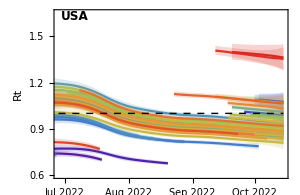
-Graphics- |

```mathematica
fig=Grid[{{countryRtPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt.png

```mathematica
finalRts=Table[If[Length[rtGather["USA",variant]]>0,rtGather["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsLower=Table[If[Length[rtGatherLower["USA",variant]]>0,rtGatherLower["USA",variant][[-1,2]],Null],{variant,variants}];
```

```mathematica
finalRtsUpper=Table[If[Length[rtGatherUpper["USA",variant]]>0,rtGatherUpper["USA",variant][[-1,2]],Null],{variant,variants}];
```

## Prevalence

```mathematica
pData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_I-combined-"<>model<>".tsv"];
```

```mathematica
header=pData[[1]]
```

{date,location,variant,median_I_smooth,I_smooth_upper_95,I_smooth_lower_95,I_smooth_upper_80,I_smooth_lower_80,I_smooth_upper_50,I_smooth_lower_50,median_freq}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_I_smooth→4,I_smooth_upper_95→5,I_smooth_lower_95→6,I_smooth_upper_80→7,I_smooth_lower_80→8,I_smooth_upper_50→9,I_smooth_lower_50→10,median_freq→11}

```mathematica
pData=Drop[pData,1];
```

Only keep data points with incidence

```mathematica
pData=Cases[pData,x_/;x[[4]]>0.9];
```

```mathematica
pGather[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
pGatherLower[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
pGatherUpper[country_,variant_]:=Cases[pData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListLogPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{200,100000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{{10,20,100,200,1000,2000,10000,20000,100000,200000,1000000},Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

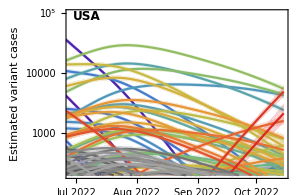
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-log-cases.png

```mathematica
variantCountryPrevalencePlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=pGather[country,variant];
lowerSeries=pGatherLower[country,variant];
upperSeries=pGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant cases"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,32000}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryPrevalencePlot[country_]:=Show[Table[variantCountryPrevalencePlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

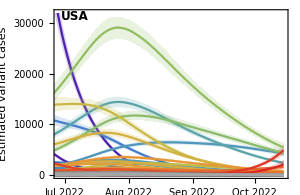
-Graphics- |

```mathematica
fig=Grid[{{countryPrevalencePlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-cases.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-cases.png

## Frequency

```mathematica
fData=Import["../../estimates/"<>dataset<>"/"<>dataset<>"_freq-combined-"<>model<>".tsv"];
```

```mathematica
header=fData[[1]]
```

{date,location,variant,median_freq,freq_upper_95,freq_lower_95,freq_upper_80,freq_lower_80,freq_upper_50,freq_lower_50}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,median_freq→4,freq_upper_95→5,freq_lower_95→6,freq_upper_80→7,freq_lower_80→8,freq_upper_50→9,freq_lower_50→10}

```mathematica
fData=Drop[fData,1];
```

```mathematica
fGather[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,4}]]
```

```mathematica
fGatherLower[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,8}]]
```

```mathematica
fGatherUpper[country_,variant_]:=Cases[fData,x_/;x[[2]]==country&&x[[3]]==variant][[All,{1,7}]]
```

```mathematica
variantCountryFrequencyPlot[country_,variant_,color_]:=Module[{medianSeries,lowerSeries,upperSeries},
medianSeries=fGather[country,variant];
lowerSeries=fGatherLower[country,variant];
upperSeries=fGatherUpper[country,variant];
DateListPlot[{medianSeries,lowerSeries,upperSeries},Frame->{True,True,False,False},FrameLabel->{"","Estimated variant frequency"},PlotTheme->"FullAxes",ImageSize->imageSize,AspectRatio->0.65,ImagePadding->{{55,5},{15,10}},Joined->True,PlotRange->{{startDate,modelEndDate},
{0,0.5}},DateTicksFormat->{"MonthNameShort"},PlotRangeClipping->True,PlotStyle->{color,None,None},FrameTicks->{{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.2}],Automatic},{dateTicks,Automatic}},Filling->2->{3},FillingStyle->Directive[Opacity[0.2],color],
Epilog->{Text[Style[country,Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]}]
]
```

```mathematica
countryFrequencyPlot[country_]:=Show[Table[variantCountryFrequencyPlot[country,variants[[i]],colors[[i]]],{i,1,n}]]
```

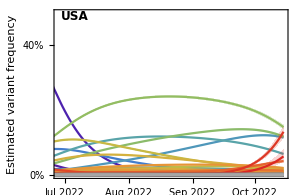
-Graphics- |

```mathematica
fig=Grid[{{countryFrequencyPlot["USA"],legendPanel}},Spacings->{1,1},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_variant-estimated-frequency.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-estimated-frequency.png

```mathematica
finalFrequencies=Table[fGather["USA",variant][[-1,2]],{variant,variants}];
```

## Rts and frequencies across variants

```mathematica
pos=Flatten[Position[finalRts,x_/;NumberQ[x]]];
```

```mathematica
finalRts=finalRts[[pos]];
```

```mathematica
finalRtsLower=finalRtsLower[[pos]];
```

```mathematica
finalRtsUpper=finalRtsUpper[[pos]];
```

```mathematica
finalFrequencies=finalFrequencies[[pos]];
```

```mathematica
finalVariants=variants[[pos]];
```

```mathematica
finalColors=colors[[pos]];
```

```mathematica
points=ListPlot[Table[{{i,finalRts[[i]]}},{i,Length[finalVariants]}],PlotStyle->finalColors];
```

```mathematica
lines=ListLinePlot[Table[{{i,finalRtsLower[[i]]},{i,finalRtsUpper[[i]]}},{i,Length[finalVariants]}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.35,ImageSize->600,PlotRange->{0.6,1.65},FrameTicks->{{Automatic,Automatic},{Table[{i,Rotate[finalVariants[[i]],Pi/2]},{i,Length[finalVariants]}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]}];
```

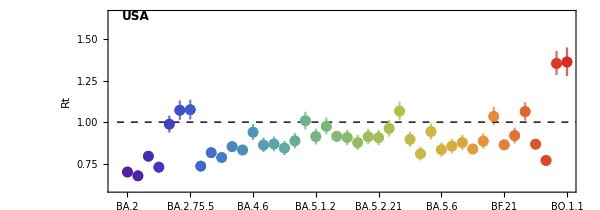

```mathematica
fig=Show[lines,points]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-listplot.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-listplot.png

```mathematica
topPos=Reverse[Ordering[finalRts,-5]];
```

```mathematica
tableValues=Table[{finalVariants[[p]],Round[finalRts[[p]],0.01],ToString[Round[finalRtsLower[[p]],0.01]]<>" - "<>ToString[Round[finalRtsUpper[[p]],0.01]]},{p,topPos}];
```

```mathematica
table=Style[TableForm[tableValues,TableHeadings->{None,{"lineage","Rt estimate","80% uncertainty interval"}},TableSpacing->{3,1}],FontFamily->"Helvetica",FontSize->12];
```

```mathematica
labels=Table[If[MemberQ[topPos,i],finalVariants[[i]],""],{i,Length[finalRts]}];
```

```mathematica
points=ListPlot[MapThread[{{#1,#2}}&,{finalFrequencies,finalRts}],PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"Current lineage frequency","Rt"},PlotStyle->Map[Directive[Opacity[0.75],#]&,finalColors],AspectRatio->0.65,ImageSize->350,PlotRange->{{0,0.15},{0.6,1.65}},FrameTicks->{{Automatic,Automatic},{Table[{i,ToString[Round[100*i]]<>"%"},{i,0,1,0.03}],Automatic}},Epilog->{Text[Style["USA",Black,FontSize->12,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}],Dashed,Black,Line[{{0,1},{n,1}}]},PlotLabels->Placed[labels,Right]];
```

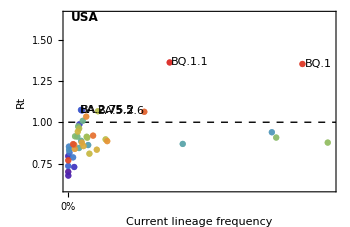
-Graphics- | lineage | Rt estimate | 80% uncertainty interval
BQ.1.1 | 1.36 | 1.28 - 1.45
BQ.1 | 1.35 | 1.28 - 1.43
BA.2.75.5 | 1.07 | 1.02 - 1.13
BA.2.75.2 | 1.07 | 1.01 - 1.13
BA.5.2.6 | 1.07 | 1.01 - 1.12

```mathematica
fig=Grid[{{points,table}}]
```

```mathematica
Export["figures/"<>dataset<>"_variant-rt-top.png",fig,"PNG",ImageResolution->300]
```

figures/pango-countries_variant-rt-top.png